## Mirror Geometry

References: 
- Tao, X. (2014), A numerical study of chorus generation and the related variation of wave intensity using the DAWN code, 
J. Geophys. Res. Space Physics, 119, 3362-3372, doi:10.1002/2014JA019820.
- Ke, Y., Gao, X., Lu, Q., Wang, X., and Wang, S. (2017), Generation of rising-tone chorus in a two-dimensional mirror field by using the general curvilinear PIC code, 
J. Geophys. Res. Space Physics, 122, 8154-8165, doi:10.1002/2017JA024178.

### Mirror Magnetic Field

We choose a Cartesian coordinate system where the origin coincides with the center of mirror geometry.
We choose the x coordinate along the mirror magnetic field at the center of mirror geometry.
Then, the x component of the background magnetic field may be written as
B_x(𝕣)=B_x(x)=B_0(1+ξ^2 x^2),
where B_0 is the mirror magnetic field at the origin and ξ is the inhomogeneity parameter and in units of inverse of length.
Consider cylindrical coordinates, (x,s,ϕ), where
x=x; 
y=s cosϕ; 
z=s sinϕ.
The unit vectors are given by
𝕖_x=𝕖_x; 
𝕖_s=cosϕ 𝕖_y+sinϕ 𝕖_z; 
𝕖_ϕ=-sinϕ 𝕖_y+cosϕ 𝕖_z.
Making use of cylindrical symmetry, the divergence-free condition of the magnetic field yields
0=∇·𝔹=(∂B_x)/(∂x)+1/s∂/(∂s)(s B_s)+1/s(∂B_ϕ)/(∂ϕ) → ∂/(∂s)(s B_s)=-s(∂B_x)/(∂x).
Integrating both sides with B_s(s=0)=0 as the boundary condition yields
(s B_s)=-(B_0 2 ξ^2 x)s^2/2
B_s=-B_0 ξ^2 x s.
We also have B_ϕ=0.
Therefore, the mirror magnetic field vector is given by 
𝔹=B_x 𝕖_x+B_s 𝕖_s
=B_x 𝕖_x+B_s cosϕ 𝕖_y+B_s sinϕ 𝕖_z.
Substituting B_s, we can get the expressions for B_y and B_z. 
Hence all three Cartesian components read
(B_x
B_y
B_z)=B_0(1+ξ^2 x^2
-ξ^2x y
-ξ^2x z).
The magnitude of the field is
B^2=B_x^2+B_s^2=B_0^2((1+ξ^2 x^2)^2+ξ^4 x^2 s^2)
=B_x^2(1+(ξ^4 x^2 s^2)/((1+ξ^2 x^2)^2)).
Note that
∇×𝔹=ξ^2 z 𝕖_y-ξ^2 y 𝕖_z.
From the condition d𝕣=dx 𝕖_x+ds 𝕖_s+s dϕ 𝕖_ϕ=k 𝔹 (k is a constant scale factor), the field line equation is given by
ϕ=const; 
dx/B_x=ds/B_s
dx/(1+ξ^2 x^2)=ds/(-ξ^2x s)
ds/s=(-ξ^2x)/(1+ξ^2 x^2)dx
Log[s]=-1/2Log[1+ξ^2 x^2]+k
s=s_0/(√(1+ξ^2 x^2))=s_0/(√(B_x(x)/B_0)),
where s_0 is an integral constant and chosen such that s(x=0)=s_0.
The Cartesian coordinates of the field line position vector are
(x
y
z)=(x
y_0/(√(1+ξ^2 x^2))
z_0/(√(1+ξ^2 x^2))).
The field line arc length (for a given s_0) is given by
d r^2=d x^2+d s^2=d x^2+(ξ^4 x^2 s_0^2)/((1+ξ^2 x^2)^3)d x^2
=(1+(ξ^4 x^2 s_0^2)/((1+ξ^2 x^2)^3))d x^2
=(1+(ξ^4 x^2 s^2)/((1+ξ^2 x^2)^2))d x^2
=B^2/B_x^2 d x^2.

```mathematica
With[{ξ=2,x=RandomReal[{-1,1}],y0=RandomReal[{-1,1}],z0=RandomReal[{-1,1}]},
Module[{calB,y,z,𝔹,drOdx},
calB=Function[{x,y,z},{1+ξ^2x^2,-ξ^2x y,-ξ^2x z}];
If[Div[calB[xx,yy,zz],{xx,yy,zz}]!=0,Print["div.B != 0"]];
y=y0/√(1+ξ^2x^2);
z=z0/√(1+ξ^2x^2);
𝔹=calB[x,y,z];
drOdx={1,-((x*y0*ξ^2)/(1+x^2*ξ^2)^(3/2)),-((x*z0*ξ^2)/(1+x^2*ξ^2)^(3/2))};
If[Chop[Norm[Divide[Cross[drOdx,𝔹],Norm[drOdx]Norm[𝔹]]]]!=0,Print["differential field line is not perp to B"]];
]
]
```

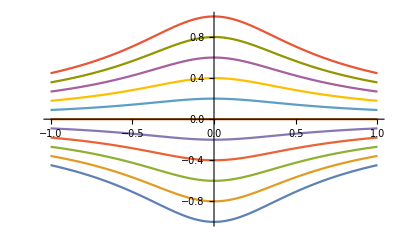

```mathematica
With[{ξ=2,z0=0,y0=Range[-1,1,.2],xlim={-1,1}},
Module[{xs,ys},
xs=Array[N,101,xlim];
ys=Divide[#,Sqrt[1+ξ^2xs^2]]&/@y0;
ListPlot[ys,DataRange->xlim,Joined->True]
]
]
```

### Curvilinear Coordinates

Let us define field line-agnostic curvilinear coordinates, (q^1,q^2,q^3).
We choose the field-aligned coordinate, q^1, such that a unit length in q^1 corresponds to a field line arc length
proportional to the mirror magnetic field. Formally,
Δ_1 ⅆ q^1=ⅆr/(B/B_0)=(B/B_x)/(B/B_0)ⅆx=B_0/B_x ⅆx=1/(1+ξ^2 x^2)ⅆx,
where Δ_1 is the scaling factor (constant) between ⅆ q^1 and ⅆx.
Integrating both sides with the boundary condition q^1(x=0)=0 yields
Δ_1 q^1=1/ξ tan^-1 ξ x.
Because the cross sectional area of the flux tube at a given location x is proportional to sⅆs or B_x^-1,
if we choose q^2 (q^3) proportional to y_0 (z_0), the volume element represented by Δ q^1 Δ q^2 Δ q^3 will remain constant.
So, similarly
Δ_2 q^2=y_0=√(1+ξ^2 x^2)y;
Δ_3 q^3=y_0=√(1+ξ^2 x^2)z.
In summary, the field-aligned curvilinear coordinates are
(Δ_1 q^1
Δ_2 q^2
Δ_3 q^3)=(1/ξ tan^-1 ξ x
√(1+ξ^2 x^2)y
√(1+ξ^2 x^2)z).
To express the Cartesian coordinates in terms of the curvilinear coordinates, notice 
x=1/ξ tan(ξ Δ_1 q^1) or ξ^2 x^2=tan^2(ξ Δ_1 q^1).
Making use of 1/(√(1+tan^2 θ))=cosθ for -π/2<θ<π/2, the Cartesian coordinates read
(x
y
z)=(1/ξ tan(ξ Δ_1 q^1)
Δ_2 q^2 cos(ξ Δ_1 q^1)
Δ_3 q^3 cos(ξ Δ_1 q^1)).
For the limiting case ξ→0, we have
(x
y
z)=(Δ_1 q^1
Δ_2 q^2
Δ_3 q^3), 
in which the meaning of the grid scaling factor Δ_j becomes clear.
The Cartesian components of the magnetic field in terms of the curvilinear coordinates are
(B_x
B_y
B_z)=B_0(1+ξ^2 x^2
-ξ^2x y
-ξ^2x z)=B_0(sec^2(ξ Δ_1 q^1)
-ξ^2 1/ξ tan(ξ Δ_1 q^1)Δ_2 q^2 cos(ξ Δ_1 q^1)
-ξ^2 1/ξ tan(ξ Δ_1 q^1)Δ_3 q^3 cos(ξ Δ_1 q^1))
=B_0(sec^2(ξ Δ_1 q^1)
-ξ Δ_2 q^2 sin(ξ Δ_1 q^1)
-ξ Δ_3 q^3 sin(ξ Δ_1 q^1)).

```mathematica
With[{ξ=2,x=RandomReal[{-1,1}],y0=RandomReal[{-1,1}],z0=RandomReal[{-1,1}]},
Module[{y,z,Bx,By,Bz,Δ1q1,Δ2q2,Δ3q3},
y=y0/√(1+ξ^2x^2);
z=z0/√(1+ξ^2x^2);
{Bx,By,Bz}={1+ξ^2x^2,-ξ^2x y,-ξ^2x z};
Δ1q1=ArcTan[ξ x]/ξ;
Δ2q2=Sqrt[1+ξ^2x^2]y;
Δ3q3=Sqrt[1+ξ^2x^2]z;
If[Chop[x-Tan[ξ Δ1q1]/ξ]!=0,Print["q1 coord invalid"]];
If[Chop[y-Δ2q2 Cos[ξ Δ1q1]]!=0,Print["q2 coord invalid"]];
If[Chop[z-Δ3q3 Cos[ξ Δ1q1]]!=0,Print["q3 coord invalid"]];
If[Chop[Bx-Sec[ξ Δ1q1]^2]!=0,Print["Bx coord invalid"]];
If[Chop[By+ξ Δ2q2 Sin[ξ Δ1q1]]!=0,Print["By coord invalid"]];
If[Chop[Bz+ξ Δ3q3 Sin[ξ Δ1q1]]!=0,Print["Bz coord invalid"]];
]
]
```

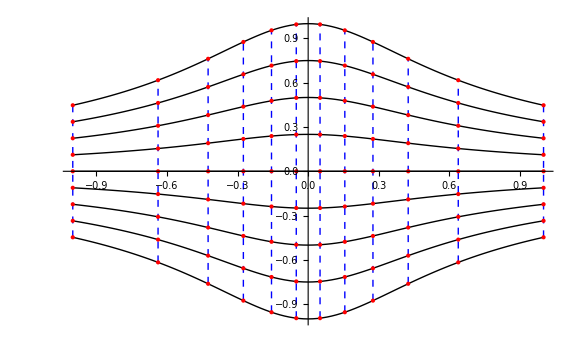

```mathematica
With[{ξ=2,z0=0,y0lim={-1,1},xlim={-1,1},nq1=12,nq2=9},
Module[{xs,ys,Δ1q1s,Δ2q2s,grid},
xs=Array[N,101,xlim];
ys=Divide[#,Sqrt[1+ξ^2xs^2]]&/@Array[N,nq2,y0lim];
Δ1q1s=Array[N,nq1,ArcTan[ξ xlim]/ξ];
Δ2q2s=Array[N,nq2,y0lim];
grid=Function[{Δ1q1,Δ2q2},{Tan[ξ Δ1q1]/ξ,Δ2q2 Cos[ξ Δ1q1]},{Listable}];
grid=grid[#,Δ2q2s]&/@Δ1q1s;
Show[
ListPlot[ys,DataRange->xlim,Joined->True,PlotStyle->Directive[Thickness[Small],Black]],
Graphics[{
{Blue,Dashed,Line/@grid},
{Red,PointSize[Medium],Point[Join@@grid]}
}],
ImageSize->Large
]
]
]
```

### Metric and Basis Vectors

Having established the relationship between the two different coordinate sets, let us now find the metric and basis vectors.
The covariant basis vectors are given by 𝕘_j=(∂𝕣)/(∂q^j):
𝕘_1=(∂𝕣)/(∂q^1)=Δ_1 sec^2(ξ Δ_1 q^1)𝕖_x-Δ_1 ξ Δ_2 q^2 sin(ξ Δ_1 q^1)𝕖_y-Δ_1 ξ Δ_3 q^3 sin(ξ Δ_1 q^1)𝕖_z
=Δ_1(sec^2(ξ Δ_1 q^1)𝕖_x-ξ Δ_2 q^2 sin(ξ Δ_1 q^1)𝕖_y-ξ Δ_3 q^3 sin(ξ Δ_1 q^1)𝕖_z)
=Δ_1((1+ξ^2 x^2)𝕖_x-ξ^2 x y 𝕖_y-ξ^2 x z 𝕖_z)
=Δ_1 𝔹/B_0;
𝕘_2=(∂𝕣)/(∂q^2)=Δ_2 cos(ξ Δ_1 q^1)𝕖_y=Δ_2/(√(1+ξ^2 x^2))=Δ_2 √(B_0/B_x)𝕖_y;
𝕘_3=(∂𝕣)/(∂q^3)=Δ_3 cos(ξ Δ_1 q^1)𝕖_z=Δ_3/(√(1+ξ^2 x^2))=Δ_3 √(B_0/B_x)𝕖_z;
where we have used
sec^2(ξ Δ_1 q^1)=1+ξ^2 x^2=B_x/B_0;
sin^2(ξ Δ_1 q^1)=1-1/(sec^2(ξ Δ_1 q^1))=(ξ^2 x^2)/(1+ξ^2 x^2).
The covariant components of the metric tensor are
g_ij=𝕘_i·𝕘_j
=(Δ_1^2 B^2/B_0^2 | Δ_1 Δ_2 √(B_0/B_x)B_y/B_0 | Δ_1 Δ_3 √(B_0/B_x)B_z/B_0
Δ_1 Δ_2 √(B_0/B_x)B_y/B_0 | Δ_2^2 B_0/B_x | 0
Δ_1 Δ_3 √(B_0/B_x)B_z/B_0 | 0 | Δ_3^2 B_0/B_x)=(Δ_1^2((1+ξ^2 x^2)^2+ξ^4 x^2 s^2) | Δ_1 Δ_2(-ξ^2x y)/(√(1+ξ^2 x^2)) | Δ_1 Δ_3(-ξ^2x z)/(√(1+ξ^2 x^2))
Δ_1 Δ_2(-ξ^2x y)/(√(1+ξ^2 x^2)) | Δ_2^2 1/(1+ξ^2 x^2) | 0
Δ_1 Δ_3(-ξ^2x z)/(√(1+ξ^2 x^2)) | 0 | Δ_3^2 1/(1+ξ^2 x^2))
=(Δ_1^2(sec^4(ξ Δ_1 q^1)+((ξ Δ_2 q^2)^2+(ξ Δ_3 q^3)^2)sin^2(ξ Δ_1 q^1)) | -Δ_1 Δ_2(ξ Δ_2 q^2)/2 sin(2ξ Δ_1 q^1) | -Δ_1 Δ_3(ξ Δ_3 q^3)/2 sin(2ξ Δ_1 q^1)
-Δ_1 Δ_2(ξ Δ_2 q^2)/2 sin(2ξ Δ_1 q^1) | Δ_2^2 cos^2(ξ Δ_1 q^1) | 0
-Δ_1 Δ_3(ξ Δ_3 q^3)/2 sin(2ξ Δ_1 q^1) | 0 | Δ_3^2 cos^2(ξ Δ_1 q^1)).
Note that
g=|g_ij|=Δ_1^2 Δ_2^2 Δ_3^2 
is independent of position.
Therefore, the differential volume element is
ⅆV=𝕘_1·(𝕘_2×𝕘_3)ⅆ q^1ⅆ q^2ⅆ q^3=Δ_1 Δ_2 Δ_3 ⅆ q^1ⅆ q^2ⅆ q^3=√g ⅆ q^1ⅆ q^2ⅆ q^3 
is also independent of position.

The contravariant basis vectors are given by 𝕘^j=∇q^j or 𝕘^i=e^ijk 𝕘_j 𝕘_k (where e^ijk=1/(√g)ϵ_ijk):
𝕘^1=1/(√g)(𝕘_2×𝕘_3)=1/Δ_1 B_0/B_x 𝕖_x=1/Δ_1 1/(1+ξ^2 x^2)𝕖_x=(cos^2(ξ Δ_1 q^1))/Δ_1 𝕖_x;
𝕘^2=1/(√g)(𝕘_3×𝕘_1)=1/Δ_2 √(B_0/B_x)(𝕖_z×𝔹/B_0)=1/Δ_2 √(B_0/B_x)(-B_y/B_0 𝕖_x+B_x/B_0 𝕖_y)=1/Δ_2((ξ^2 x y)/(√(1+ξ^2 x^2))𝕖_x+√(1+ξ^2 x^2)𝕖_y)
=1/Δ_2(ξ Δ_2 q^2 sin(ξ Δ_1 q^1)cos(ξ Δ_1 q^1)𝕖_x+sec(ξ Δ_1 q^1)𝕖_y)=1/Δ_2(ξ Δ_2 q^2(sin(2ξ Δ_1 q^1))/2 𝕖_x+sec(ξ Δ_1 q^1)𝕖_y);
𝕘^3=1/(√g)(𝕘_1×𝕘_2)=1/Δ_3 √(B_0/B_x)(𝔹/B_0×𝕖_y)=1/Δ_3 √(B_0/B_x)(-B_z/B_0 𝕖_x+B_x/B_0 𝕖_z)=1/Δ_3((ξ^2 x z)/(√(1+ξ^2 x^2))𝕖_x+√(1+ξ^2 x^2)𝕖_z)
=1/Δ_3(ξ Δ_3 q^3 sin(ξ Δ_1 q^1)cos(ξ Δ_1 q^1)𝕖_x+sec(ξ Δ_1 q^1)𝕖_z)=1/Δ_3(ξ Δ_3 q^3(sin(2ξ Δ_1 q^1))/2 𝕖_x+sec(ξ Δ_1 q^1)𝕖_z);
The contravariant components of the metric tensor are
g^ij=𝕘^i·𝕘^j
=(1/Δ_1^2 B_0^2/B_x^2 | -1/(Δ_1 Δ_2)B_y/B_x √(B_0/B_x) | -1/(Δ_1 Δ_3)B_z/B_x √(B_0/B_x)
-1/(Δ_1 Δ_2)B_y/B_x √(B_0/B_x) | 1/Δ_2^2 B_0/B_x(B_x^2/B_0^2+B_y^2/B_0^2) | 1/(Δ_2 Δ_3)B_0/B_x((B_y B_z)/B_0^2)
-1/(Δ_1 Δ_3)B_z/B_x √(B_0/B_x) | 1/(Δ_2 Δ_3)B_0/B_x((B_y B_z)/B_0^2) | 1/Δ_3^2 B_0/B_x(B_x^2/B_0^2+B_z^2/B_0^2))=(1/Δ_1^2 1/((1+ξ^2 x^2)^2) | 1/(Δ_1 Δ_2)(ξ^2 x y)/((1+ξ^2 x^2)^(3/2)) | 1/(Δ_1 Δ_3)(ξ^2 x z)/((1+ξ^2 x^2)^(3/2))
1/(Δ_1 Δ_2)(ξ^2 x y)/((1+ξ^2 x^2)^(3/2)) | 1/Δ_2^2((1+ξ^2 x^2)^2+ξ^4 x^2 y^2)/(1+ξ^2 x^2) | 1/(Δ_2 Δ_3)(ξ^4 x^2 y z)/(1+ξ^2 x^2)
1/(Δ_1 Δ_3)(ξ^2 x z)/((1+ξ^2 x^2)^(3/2)) | 1/(Δ_2 Δ_3)(ξ^4 x^2 y z)/(1+ξ^2 x^2) | 1/Δ_3^2((1+ξ^2 x^2)^2+ξ^4 x^2 z^2)/(1+ξ^2 x^2))
=((cos^4(ξ Δ_1 q^1))/Δ_1^2 | (cos^2(ξ Δ_1 q^1))/(Δ_1 Δ_2)(ξ Δ_2 q^2)/2 sin(2ξ Δ_1 q^1) | (cos^2(ξ Δ_1 q^1))/(Δ_1 Δ_3)(ξ Δ_3 q^3)/2 sin(2ξ Δ_1 q^1)
(cos^2(ξ Δ_1 q^1))/(Δ_1 Δ_2)(ξ Δ_2 q^2)/2 sin(2ξ Δ_1 q^1) | 1/Δ_2^2(((ξ Δ_2 q^2)/2 sin(2ξ Δ_1 q^1))^2+sec^2(ξ Δ_1 q^1)) | 1/(Δ_2 Δ_3)((ξ Δ_2 q^2)/2 sin(2ξ Δ_1 q^1))((ξ Δ_3 q^3)/2 sin(2ξ Δ_1 q^1))
(cos^2(ξ Δ_1 q^1))/(Δ_1 Δ_3)(ξ Δ_3 q^3)/2 sin(2ξ Δ_1 q^1) | 1/(Δ_2 Δ_3)((ξ Δ_2 q^2)/2 sin(2ξ Δ_1 q^1))((ξ Δ_3 q^3)/2 sin(2ξ Δ_1 q^1)) | 1/Δ_3^2(((ξ Δ_3 q^3)/2 sin(2ξ Δ_1 q^1))^2+sec^2(ξ Δ_1 q^1))).
Note that g=1/|g^ij| and 𝕘^1·(𝕘^2×𝕘^3)=1/(√g).
The field-aligned unit vector is 𝕖_∥=𝕘_1/(|𝕘_1|)=𝔹/B. 
But, the perpendicular component is not easy to define because 𝕘^2·𝕘^3≠0 in general.

```mathematica
With[{ξ=2,Δ1=.3,Δ2=.398,Δ3=.2938,x=RandomReal[{-1,1}],y0=RandomReal[{-1,1}],z0=RandomReal[{-1,1}]},
Module[{y,z,BOB0,Δ1q1,Δ2q2,Δ3q3,g1,g2,g3,gij,tmp,h1,h2,h3,hij},
y=y0/√(1+ξ^2x^2);
z=z0/√(1+ξ^2x^2);
Δ1q1=ArcTan[ξ x]/ξ;
Δ2q2=Sqrt[1+ξ^2x^2]y;
Δ3q3=Sqrt[1+ξ^2x^2]z;
BOB0={1+ξ^2x^2,-ξ^2x y,-ξ^2x z};
(**)
g1=Δ1 BOB0;
If[Chop[Norm[g1-Δ1{Sec[ξ Δ1q1]^2,-ξ Δ2q2 Sin[ξ Δ1q1],-ξ Δ3q3 Sin[ξ Δ1q1]}]]!=0,
Print["g1-Δ1{Sec[ξ Δ1q1]^2,-ξ Δ2q2 Sin[ξ Δ1q1],-ξ Δ3q3 Sin[ξ Δ1q1]}"]];
g2={0,Δ2 √(1/BOB0[[1]]),0};
If[Chop[Norm[g2-Δ2{0,Cos[ξ Δ1q1],0}]]!=0,Print["g2-Δ2{0,Cos[ξ Δ1q1],0}"]];
g3={0,0,Δ3 √(1/BOB0[[1]])};
If[Chop[Norm[g3-Δ3{0,0,Cos[ξ Δ1q1]}]]!=0,Print["g3-Δ3{0,0,Cos[ξ Δ1q1]}"]];
If[Chop[Δ1 Δ2 Δ3-g1.Cross[g2,g3]]!=0,Print["Δ1 Δ2 Δ3-g1.Cross[g2,g3]"]];
gij=({{Δ1^2Norm[BOB0]^2, Δ1 Δ2 BOB0[[2]]/√BOB0[[1]], Δ1 Δ3 BOB0[[3]]/√BOB0[[1]]}, {Δ1 Δ2 BOB0[[2]]/√BOB0[[1]], Δ2^2/BOB0[[1]], 0}, {Δ1 Δ3 BOB0[[3]]/√BOB0[[1]], 0, Δ3^2/BOB0[[1]]}});
If[Chop[Norm[gij-{{g1.g1,g1.g2,g1.g3},{g2.g1,g2.g2,g2.g3},{g3.g1,g3.g2,g3.g3}}]]!=0,
Print["gij-{{g1.g1,g1.g2,g1.g3},{g2.g1,g2.g2,g2.g3},{g3.g1,g3.g2,g3.g3}}"]];
If[Chop[Δ1^2Δ2^2Δ3^2-Det[gij]]!=0,Print["Δ1^2Δ2^2Δ3^2-Det[gij]"]];
tmp={
{Δ1^2(Sec[ξ Δ1q1]^4+((ξ Δ2q2)^2+(ξ Δ3q3)^2)Sin[ξ Δ1q1]^2),-Δ1 Δ2 ξ Δ2q2 Sin[2ξ Δ1q1]/2,-Δ1 Δ3 ξ Δ3q3 Sin[2ξ Δ1q1]/2},
{-Δ1 Δ2 ξ Δ2q2 Sin[2ξ Δ1q1]/2,Δ2^2Cos[ξ Δ1q1]^2,0},
{-Δ1 Δ3 ξ Δ3q3 Sin[2ξ Δ1q1]/2,0,Δ3^2Cos[ξ Δ1q1]^2}
};
If[Chop[Norm[gij-tmp]]!=0,Print["gij-gij(curvi)"]];
(**)
h1={1/BOB0[[1]],0,0}/Δ1;
If[Chop[Norm[h1-Cross[g2,g3]/√Det[gij]]]!=0,Print["h1-Cross[g2,g3]/√Det[gij]"]];
h2={-BOB0[[2]],BOB0[[1]],0}/Δ2/√BOB0[[1]];
If[Chop[Norm[h2-Cross[g3,g1]/√Det[gij]]]!=0,Print["h2-Cross[g3,g1]/√Det[gij]"]];
h3={-BOB0[[3]],0,BOB0[[1]]}/Δ3/√BOB0[[1]];
If[Chop[Norm[h3-Cross[g1,g2]/√Det[gij]]]!=0,Print["h3-Cross[g1,g2]/√Det[gij]"]];
tmp={Cos[ξ Δ1q1]^2,0,0}/Δ1;
If[Chop[Norm[h1-tmp]]!=0,Print["h1-h1(curvi)"]];
tmp={ξ Δ2q2 Sin[2ξ Δ1q1]/2,Sec[ξ Δ1q1],0}/Δ2;
If[Chop[Norm[h2-tmp]]!=0,Print["h2-h2(curvi)"]];
tmp={ξ Δ3q3 Sin[2ξ Δ1q1]/2,0,Sec[ξ Δ1q1]}/Δ3;
If[Chop[Norm[h3-tmp]]!=0,Print["h3-h3(curvi)"]];
hij=({{1/(Δ1^2BOB0[[1]]^2), -1/(Δ1 Δ2)BOB0[[2]]/(BOB0[[1]] √BOB0[[1]]), -1/(Δ1 Δ3)BOB0[[3]]/(BOB0[[1]] √BOB0[[1]])}, {-1/(Δ1 Δ2)BOB0[[2]]/(BOB0[[1]] √BOB0[[1]]), (BOB0[[1]]^2+BOB0[[2]]^2)/(Δ2^2BOB0[[1]]), (BOB0[[2]]BOB0[[3]])/(Δ2 Δ3 BOB0[[1]])}, {-1/(Δ1 Δ3)BOB0[[3]]/(BOB0[[1]] √BOB0[[1]]), (BOB0[[2]]BOB0[[3]])/(Δ2 Δ3 BOB0[[1]]), (BOB0[[1]]^2+BOB0[[3]]^2)/(Δ3^2BOB0[[1]])}});
If[Chop[Norm[hij-{{h1.h1,h1.h2,h1.h3},{h2.h1,h2.h2,h2.h3},{h3.h1,h3.h2,h3.h3}}]]!=0,
Print["hij-{{h1.h1,h1.h2,h1.h3},{h2.h1,h2.h2,h2.h3},{h3.h1,h3.h2,h3.h3}}"]];
If[Chop[Δ1^2Δ2^2Δ3^2-1/Det[hij]]!=0,Print["Δ1^2Δ2^2Δ3^2-1/Det[hij]"]];
tmp={
{Cos[ξ Δ1q1]^4/Δ1^2,Cos[ξ Δ1q1]^2/(Δ1 Δ2)(ξ Δ2q2)/2 Sin[2ξ Δ1q1],Cos[ξ Δ1q1]^2/(Δ1 Δ3)(ξ Δ3q3)/2 Sin[2ξ Δ1q1]},
{Cos[ξ Δ1q1]^2/(Δ1 Δ2)(ξ Δ2q2)/2 Sin[2ξ Δ1q1],1/Δ2^2(((ξ Δ2q2)/2 Sin[2ξ Δ1q1])^2+Sec[ξ Δ1q1]^2),1/(Δ2 Δ3)((ξ Δ2q2)/2(ξ Δ3q3)/2)Sin[2ξ Δ1q1]^2},
{Cos[ξ Δ1q1]^2/(Δ1 Δ3)(ξ Δ3q3)/2 Sin[2ξ Δ1q1],1/(Δ2 Δ3)((ξ Δ2q2)/2(ξ Δ3q3)/2)Sin[2ξ Δ1q1]^2,1/Δ3^2(((ξ Δ3q3)/2 Sin[2ξ Δ1q1])^2+Sec[ξ Δ1q1]^2)}
};
If[Chop[Norm[hij-tmp]]!=0,Print["hij-hij(curvi)"]];
If[Chop[Norm[gij.hij-IdentityMatrix[3]]]!=0,Print["gij.hij!=identity"]]
]
]
```

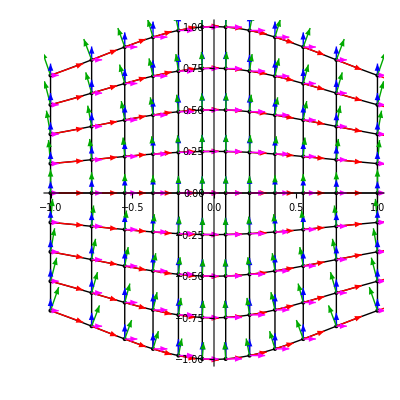

```mathematica
With[{ξ=1.,z0=0,y0lim={-1,1},xlim={-1,1},nq1=12,nq2=9,Δ1=.1,Δ2=.1},
Module[{xs,ys,Δ1q1s,Δ2q2s,grid,g1s,g2s,h1s,h2s},
xs=Array[N,101,xlim];
ys=Divide[#,Sqrt[1+ξ^2xs^2]]&/@Array[N,nq2,y0lim];
Δ1q1s=Array[N,nq1,ArcTan[ξ xlim]/ξ];
Δ2q2s=Array[N,nq2,y0lim];
grid=Function[{Δ1q1,Δ2q2},{Tan[ξ Δ1q1]/ξ,Δ2q2 Cos[ξ Δ1q1]},{Listable}];
grid=grid[#,Δ2q2s]&/@Δ1q1s;
g1s=Apply[Function[{x,y},Δ1{1+ξ^2x^2,-ξ^2x y}],grid,{2}];
g2s=Apply[Function[{x,y},Δ2{0,1/√(1+ξ^2x^2)}],grid,{2}];
h1s=Apply[Function[{x,y},Δ1{1/(1+ξ^2x^2),0}],grid,{2}];
h2s=Apply[Function[{x,y},Δ2{ξ^2x y/√(1+ξ^2x^2),√(1+ξ^2x^2)}],grid,{2}];
Show[
ListPlot[ys,DataRange->xlim,Joined->True,PlotStyle->Directive[Thickness[Small],Black]],
ListPlot[grid,Joined->True,PlotStyle->Directive[Thickness[Small],Black]],
Graphics[{
{Black,PointSize[Medium],Point[Join@@grid]},
{Red,Arrowheads[Small],MapThread[Arrow[{#1,Plus[##]}]&,{Join@@grid,Join@@g1s}]},
{Blue,Arrowheads[Small],MapThread[Arrow[{#1,Plus[##]}]&,{Join@@grid,Join@@g2s}]},
{Magenta,Arrowheads[Small],MapThread[Arrow[{#1,Plus[##]}]&,{Join@@grid,Join@@h1s}]},
{Darker@Green,Arrowheads[Small],MapThread[Arrow[{#1,Plus[##]}]&,{Join@@grid,Join@@h2s}]}
}],
ImageSize->400,
PlotRange->{xlim,y0lim},
PlotRangePadding->Scaled[.05],
AspectRatio->1/1
]
]
]
```

### Vector Transformations

Consider a vector 
𝕍=V_x 𝕖_x+V_y 𝕖_y+V_z 𝕖_z=V_x 𝕖_x+V_s 𝕖_s+V_ϕ 𝕖_ϕ
=V^j 𝕘_j=V_j 𝕘^j.
- From Cartesian to cylindrical:
V_x=𝕍·𝕖_x=(V_x 𝕖_x+V_y 𝕖_y+V_z 𝕖_z)·𝕖_x=𝕖_x·𝕖_x V_x+𝕖_y·𝕖_x V_y+𝕖_z·𝕖_x V_z
V_s=𝕍·𝕖_s=(V_x 𝕖_x+V_y 𝕖_y+V_z 𝕖_z)·𝕖_s=𝕖_x·𝕖_s V_x+𝕖_y·𝕖_s V_y+𝕖_z·𝕖_s V_z
V_ϕ=𝕍·𝕖_ϕ=(V_x 𝕖_x+V_y 𝕖_y+V_z 𝕖_z)·𝕖_ϕ=𝕖_x·𝕖_ϕ V_x+𝕖_y·𝕖_ϕ V_y+𝕖_z·𝕖_ϕ V_z,
or in matrix form,
(V_x
V_s
V_ϕ)=(𝕖_x·𝕖_x | 𝕖_y·𝕖_x | 𝕖_z·𝕖_x
𝕖_x·𝕖_s | 𝕖_y·𝕖_s | 𝕖_z·𝕖_s
𝕖_x·𝕖_ϕ | 𝕖_y·𝕖_ϕ | 𝕖_z·𝕖_ϕ)(V_x
V_y
V_z)=(1 | 0 | 0
0 | cosϕ | sinϕ
0 | -sinϕ | cosϕ)(V_x
V_y
V_z)=𝔏_(𝕩→(x,s,ϕ))(V_x
V_y
V_z).
- From cylindrical to Cartesian:
(V_x
V_y
V_z)=(𝕖_x·𝕖_x | 𝕖_s·𝕖_x | 𝕖_ϕ·𝕖_x
𝕖_x·𝕖_y | 𝕖_s·𝕖_y | 𝕖_ϕ·𝕖_y
𝕖_x·𝕖_z | 𝕖_s·𝕖_z | 𝕖_ϕ·𝕖_z)(V_x
V_s
V_ϕ)=𝔏_((x,s,ϕ)→𝕩)(V_x
V_s
V_ϕ)=𝔏_(𝕩→(x,s,ϕ))ᵀ(V_x
V_s
V_ϕ)=(V_x | V_s | V_ϕ)𝔏_(𝕩→(x,s,ϕ)).
- From Cartesian to curvilinear contravariant:
V^j=𝕘^j·𝕍;
or in matrix form,
(V^1
V^2
V^3)=(𝕘^1·𝕖_x | 𝕘^1·𝕖_y | 𝕘^1·𝕖_z
𝕘^2·𝕖_x | 𝕘^2·𝕖_y | 𝕘^2·𝕖_z
𝕘^3·𝕖_x | 𝕘^3·𝕖_y | 𝕘^3·𝕖_z)(V_x
V_y
V_z)=𝔏_(𝕩→V^j)(V_x
V_y
V_z),
where
𝔏_(𝕩→V^j)=(1/Δ_1 B_0/B_x | 0 | 0
-1/Δ_2 √(B_0/B_x)B_y/B_0 | 1/Δ_2 √(B_x/B_0) | 0
-1/Δ_3 √(B_0/B_x)B_z/B_0 | 0 | 1/Δ_3 √(B_x/B_0))=(1/Δ_1 1/(1+ξ^2 x^2) | 0 | 0
1/Δ_2(ξ^2 x y)/(√(1+ξ^2 x^2)) | (√(1+ξ^2 x^2))/Δ_2 | 0
1/Δ_3(ξ^2 x z)/(√(1+ξ^2 x^2)) | 0 | (√(1+ξ^2 x^2))/Δ_3)=((cos^2(ξ Δ_1 q^1))/Δ_1 | 0 | 0
(ξ Δ_2 q^2)/Δ_2(sin(2ξ Δ_1 q^1))/2 | (sec(ξ Δ_1 q^1))/Δ_2 | 0
(ξ Δ_3 q^3)/Δ_3(sin(2ξ Δ_1 q^1))/2 | 0 | (sec(ξ Δ_1 q^1))/Δ_3).
- From curvilinear covariant to Cartesian: Using 𝕍=V_j 𝕘^j
(V_x
V_y
V_z)=(𝕖_x·𝕘^1 | 𝕖_x·𝕘^2 | 𝕖_x·𝕘^3
𝕖_y·𝕘^1 | 𝕖_y·𝕘^2 | 𝕖_y·𝕘^3
𝕖_z·𝕘^1 | 𝕖_z·𝕘^2 | 𝕖_z·𝕘^3)(V_1
V_2
V_3)=𝔏_(V_j→𝕩)(V_1
V_2
V_3)=𝔏_(𝕩→V^j)ᵀ(V_1
V_2
V_3)=(V_1 | V_2 | V_3)𝔏_(𝕩→V^j).
- From Cartesian to curvilinear covariant:
V_j=𝕘_j·𝕍;
or in matrix form,
(V_1
V_2
V_3)=(𝕘_1·𝕖_x | 𝕘_1·𝕖_y | 𝕘_1·𝕖_z
𝕘_2·𝕖_x | 𝕘_2·𝕖_y | 𝕘_2·𝕖_z
𝕘_3·𝕖_x | 𝕘_3·𝕖_y | 𝕘_3·𝕖_z)(V_x
V_y
V_z)=𝔏_(𝕩→V_j)(V_x
V_y
V_z),
where
𝔏_(𝕩→V_j)=(Δ_1 B_x/B_0 | Δ_1 B_y/B_0 | Δ_1 B_z/B_0
0 | Δ_2 √(B_0/B_x) | 0
0 | 0 | Δ_3 √(B_0/B_x))=(Δ_1(1+ξ^2 x^2) | -Δ_1 ξ^2 x y | -Δ_1 ξ^2 x z
0 | Δ_2/(√(1+ξ^2 x^2)) | 0
0 | 0 | Δ_3/(√(1+ξ^2 x^2)))=(Δ_1 sec^2(ξ Δ_1 q^1) | -Δ_1(ξ Δ_2 q^2)sin(ξ Δ_1 q^1) | -Δ_1(ξ Δ_3 q^3)sin(ξ Δ_1 q^1)
0 | Δ_2 cos(ξ Δ_1 q^1) | 0
0 | 0 | Δ_3 cos(ξ Δ_1 q^1)).
- From curvilinear contravariant to Cartesian: Using 𝕍=V^j 𝕘_j
(V_x
V_y
V_z)=(𝕖_x·𝕘_1 | 𝕖_x·𝕘_2 | 𝕖_x·𝕘_3
𝕖_y·𝕘_1 | 𝕖_y·𝕘_2 | 𝕖_y·𝕘_3
𝕖_z·𝕘_1 | 𝕖_z·𝕘_2 | 𝕖_z·𝕘_3)(V^1
V^2
V^3)=𝔏_(V^j→𝕩)(V^1
V^2
V^3)=𝔏_(𝕩→V_j)ᵀ(V^1
V^2
V^3)=(V^1 | V^2 | V^3)𝔏_(𝕩→V_j).
- From contravariant to covariant: 
V_i=𝕘_i·(V^j 𝕘_j)=𝕘_i·𝕘_j V^j=g_ij V^j.
- From covariant to contravariant: 
V^i=𝕘^i·(V_j 𝕘^j)=𝕘^i·𝕘^j V_j=g^ij V_j.

```mathematica
With[{ξ=2,Δ1=.3,Δ2=.398,Δ3=.2938,x=.6,y0=.35,z0=-.45,vcarts={.49584,-.49483,383763}},
Module[{y,z,Δ1q1,Δ2q2,Δ3q3,BOB0,g1,g2,g3,gij,h1,h2,h3,hij,Lcarts2contr,tmp,Lcarts2covar},
y=y0/√(1+ξ^2x^2);
z=z0/√(1+ξ^2x^2);
Δ1q1=ArcTan[ξ x]/ξ;
Δ2q2=Sqrt[1+ξ^2x^2]y;
Δ3q3=Sqrt[1+ξ^2x^2]z;
BOB0={1+ξ^2x^2,-ξ^2x y,-ξ^2x z};
(**)
g1=Δ1 BOB0;
g2={0,Δ2 √(1/BOB0[[1]]),0};
g3={0,0,Δ3 √(1/BOB0[[1]])};
gij=({{Δ1^2Norm[BOB0]^2, Δ1 Δ2 BOB0[[2]]/√BOB0[[1]], Δ1 Δ3 BOB0[[3]]/√BOB0[[1]]}, {Δ1 Δ2 BOB0[[2]]/√BOB0[[1]], Δ2^2/BOB0[[1]], 0}, {Δ1 Δ3 BOB0[[3]]/√BOB0[[1]], 0, Δ3^2/BOB0[[1]]}});
(**)
h1={1/BOB0[[1]],0,0}/Δ1;
h2={-BOB0[[2]],BOB0[[1]],0}/Δ2/√BOB0[[1]];
h3={-BOB0[[3]],0,BOB0[[1]]}/Δ3/√BOB0[[1]];
hij=({{1/(Δ1^2BOB0[[1]]^2), -1/(Δ1 Δ2)BOB0[[2]]/(BOB0[[1]] √BOB0[[1]]), -1/(Δ1 Δ3)BOB0[[3]]/(BOB0[[1]] √BOB0[[1]])}, {-1/(Δ1 Δ2)BOB0[[2]]/(BOB0[[1]] √BOB0[[1]]), (BOB0[[1]]^2+BOB0[[2]]^2)/(Δ2^2BOB0[[1]]), (BOB0[[2]]BOB0[[3]])/(Δ2 Δ3 BOB0[[1]])}, {-1/(Δ1 Δ3)BOB0[[3]]/(BOB0[[1]] √BOB0[[1]]), (BOB0[[2]]BOB0[[3]])/(Δ2 Δ3 BOB0[[1]]), (BOB0[[1]]^2+BOB0[[3]]^2)/(Δ3^2BOB0[[1]])}});
(**)
Lcarts2contr=({{1/(Δ1 BOB0[[1]]), 0, 0}, {-1/Δ2 BOB0[[2]]/(√BOB0[[1]]), (√BOB0[[1]])/Δ2, 0}, {-1/Δ3 BOB0[[3]]/(√BOB0[[1]]), 0, (√BOB0[[1]])/Δ3}});
tmp=({{Cos[ξ Δ1q1]^2/Δ1, 0, 0}, {(ξ Δ2q2)/Δ2 Sin[2ξ Δ1q1]/2, Sec[ξ Δ1q1]/Δ2, 0}, {(ξ Δ3q3)/Δ3 Sin[2ξ Δ1q1]/2, 0, Sec[ξ Δ1q1]/Δ3}});
If[Chop[Norm[Lcarts2contr-tmp]]!=0,Print["Lcarts2contr-Lcarts2contr(curvi)"]];
Lcarts2covar=({{Δ1 BOB0[[1]], Δ1 BOB0[[2]], Δ1 BOB0[[3]]}, {0, Δ2/√BOB0[[1]], 0}, {0, 0, Δ3/√BOB0[[1]]}});
tmp=({{Δ1 Sec[ξ Δ1q1]^2, -Δ1(ξ Δ2q2)Sin[ξ Δ1q1], -Δ1(ξ Δ3q3)Sin[ξ Δ1q1]}, {0, Δ2 Cos[ξ Δ1q1], 0}, {0, 0, Δ3 Cos[ξ Δ1q1]}});
If[Chop[Norm[Lcarts2covar-tmp]]!=0,Print["Lcarts2covar-Lcarts2covar(curvi)"]];
If[Chop[Norm[Lcarts2contr.(Lcarts2covarᵀ)-IdentityMatrix[3]]]!=0,Print["Lcarts2contr.(Lcarts2covarᵀ)-IdentityMatrix[3]"]];
If[Chop[Norm[vcarts-(Lcarts2contr.vcarts).Lcarts2covar]]!=0,Print["vcarts-(Lcarts2contr.vcarts).Lcarts2covar"]];
If[Chop[Norm[vcarts-(Lcarts2covar.vcarts).Lcarts2contr]]!=0,Print["vcarts-(Lcarts2covar.vcarts).Lcarts2contr"]];
If[Chop[Norm[vcarts-(gij.vcarts).hij]]!=0,Print["vcarts-(gij.vcarts).hij"]]
]
]
```

## Mirror Motion

Mirroring motion in 1D simulations is achieved as follows.
The magnetic field seen by a particle is calculated at
𝕣=ℝ+𝕣_L,
where ℝ is the guiding center location and
𝕣_L=-𝕧/Ω×𝔹/B≈-𝕧/Ω×𝕖_x,
where
Ω=q/(m c)B(𝕣)≈(q B_0)/(m c)(B_x(ℝ))/B_0=Ω_0(1+ξ^2 x^2).
For the relativistic case, replace 𝕧 with 𝕦=γ 𝕧 (and m is the rest mass).

```mathematica
Clear[compileBorisC]
(*non-relativistic*)
compileBorisC[B0:{__Real}/;Length[B0]==3]:=With[{ϵ=1.*^-5},
Compile[{{v0,_Real,1},{cE,_Real,1},{dB,_Real,1},{dt,_Real}},
(*Function[{v0,cE,dB,dt},*)
Module[{𝕥=.5dt (B0+dB),v=v0,t,𝕓,v1},
v+=.5dt cE;
v=If[(t=Sqrt[𝕥.𝕥])<ϵ,
(*small angle expantion*)
Times[2,Cross[v,𝕥]+v.𝕥 𝕥-t^2v]+v
,
(*exact solution*)
𝕓=𝕥/t;
v1=(v.𝕓)𝕓;
v1+((v-v1)Cos[2t]+Cross[v,𝕓]Sin[2t])
];
v+=.5dt cE
]
]
]
(*relativistic*)
compileBorisC[c_Real?Positive,B0:{__Real}/;Length[B0]==3]:=With[{ϵ=1.*^-5},
Compile[{{γv0,_Real,1},{cE,_Real,1},{dB,_Real,1},{dt,_Real}},
(*Function[{γv0,cE,dB,dt},*)
Module[{𝕥=.5dt (B0+dB),γv=γv0,t,𝕓,v1,v},
γv+=.5dt cE;
𝕥/=Sqrt[1+Total[(γv/c)^2]];
γv=If[(t=Sqrt[𝕥.𝕥])<ϵ,
(*small angle expantion*)
Times[2,Cross[γv,𝕥]+γv.𝕥 𝕥-t^2γv]+γv
,
(*exact solution*)
𝕓=𝕥/t;
v1=(γv.𝕓)𝕓;
v1+((γv-v1)Cos[2t]+Cross[γv,𝕓]Sin[2t])
];
γv+=.5dt cE
]
]
]
```

```mathematica
Clear[compileMirrorField]
compileMirrorField[B0_?Positive,ξ_?NonNegative]:=Compile[{{xyz,_Real,1}},
Module[{x,y,z},
{x,y,z}=xyz;
B0{1+ξ^2x^2,-ξ^2x y,-ξ^2x z}
],
Parallelization->True,
RuntimeAttributes->{Listable}
]
```

```mathematica
Clear[drawFieldLine]
drawFieldLine[ξ_?NonNegative,y0lim:{_?NumberQ,_?NumberQ},xlim:{_?NumberQ,_?NumberQ}]:=With[{z0=0},
Module[{xs,ys},
xs=Array[N,101,xlim];
ys=Divide[#,Sqrt[1+ξ^2xs^2]]&/@Array[N,2,y0lim];
Show[
ListPlot[ys,DataRange->xlim,Joined->True,PlotStyle->Directive[Blue,Thickness[Medium]]],
AspectRatio->1/Apply[Divide,Subtract@@@{xlim,y0lim}],
ImageSize->Large
]
]
]
```

```mathematica
With[{Ω0=2Pi,ωb0=.05*2Pi,x0=0,v0=2Pi,α0=N[70Degree],ϕ0=N[0Degree]},
(*With[{Ω0=1,ωb0=.05,x0=0,v0=1,α0=N[60Degree],ϕ0=N[0Degree]},*)
Module[{ξ,mirrorField,boris,Δt,nt,vv,xx},
ξ=ωb0/v0;
mirrorField=compileMirrorField[Ω0,ξ];
boris=compileBorisC[{0,0,0}//N];
Δt=2.Pi/Ω0/100;
nt=Times[2.Pi/Ω0/Δt,2Ω0/ωb0]//Ceiling;
vv={v0 Cos[α0],v0 Sin[α0]Cos[ϕ0],v0 Sin[α0]Sin[ϕ0]};
xx={x0,0,0};
xx=xx-Divide[Cross[vv,{1,0,0}],Norm[mirrorField[xx]]];
{xx,vv}=NestList[Function[
xx=#[[1]];
vv=#[[2]];
xx+=.5vv Δt;
vv=boris[vv,{0,0,0},mirrorField[xx],Δt];
xx+=.5vv Δt;
{xx,vv}
],{xx,vv},nt]ᵀ;
{
Show[
Graphics[{
Line[Most/@xx],
{PointSize[Large],Blue,Point[xx[[1]]//Most],Red,Point[xx[[-1]]//Most]}
}],
drawFieldLine[ξ,MinMax[xx[[All,2]]],MinMax[xx[[All,1]]]],
AspectRatio->1/2,
ImageSize->Medium
],
ListPlot[First/@xx,DataRange->Δt{0,nt},Joined->True,ImageSize->Medium]
}
]
]
```

```mathematica
With[{Ω0=2Pi,ωb0=.05*2Pi,x0=0,v0=2Pi,α0=N[70Degree],ϕ0=N[0Degree]},
(*With[{Ω0=1,ωb0=.05,x0=0,v0=1,α0=N[60Degree],ϕ0=N[0Degree]},*)
Module[{ξ,mirrorField,boris,Δt,nt,vv,x},
ξ=ωb0/v0;
mirrorField=compileMirrorField[Ω0,ξ];
boris=compileBorisC[{0,0,0}//N];
Δt=2.Pi/Ω0/100;
nt=Times[2.Pi/Ω0/Δt,2Ω0/ωb0]//Ceiling;
vv={v0 Cos[α0],v0 Sin[α0]Cos[ϕ0],v0 Sin[α0]Sin[ϕ0]};
x=x0;
{x,vv}=NestList[Function[Module[{xx},
x=#[[1]];
vv=#[[2]];
x+=.5vv[[1]] Δt;
xx={x,0,0};
(*xx=xx-Divide[Cross[vv,{1,0,0}],Norm[mirrorField[xx]]];*)
xx=xx-Divide[Cross[vv,{1,0,0}],Ω0(1+ξ^2x^2)];
vv=boris[vv,{0,0,0},mirrorField[xx],Δt];
x+=.5vv[[1]] Δt;
{x,vv}
]],{x,vv},nt]ᵀ;
ListPlot[x,DataRange->Δt{0,nt},Joined->True,ImageSize->Medium]
]
]
```